```mathematica
(*** Fighting Fantasy combat analysis -- visualising optimal strategies ***)
```

```mathematica
(*** read optimal strategies from stochastic optimal control analysis ***)
```

```mathematica
SetDirectory["~/Dropbox/Documents/2019_Projects/Final/fighting-fantasy-analysis-master"]
```

/home/iain/Dropbox/Documents/2019_Projects/Final/fighting-fantasy-analysis-master

```mathematica
(* large == 1 : full plot *)
(* amplify == 3 or 4 : different systems from text *)
```

```mathematica
large = 0;
amplify = 3;
```

```mathematica
list = ReadList["optimal-strategies-"<>ToString[amplify]<>".txt", {Number, Number, Number, Number, Number, Number}];
```

```mathematica
(*** set graphics options ***)
```

```mathematica
myHue[x_]:=Lighter[ColorData["ThermometerColors"][x]]
```

```mathematica
(*** decide what set of parameters to plot ***)
```

```mathematica
If[large == 1, 
dset = {-9,-8,-7, -6,-5,-4,-3 -2, -1, 0, 1, 2, 3,4,5,6,7,8, 9};
lset = {0, 12, 11, 10, 9,8, 7, 6, 5, 4, 3, 2, 1, 0};
,
dset = {-4, -2, 0, 2, 4};
lset = {0, 12,9,6,3};
];
```

```mathematica
(*** produce trellis of summary plots ***)
```

```mathematica
gset = Table[Table[{}, {i, 1, Length[lset]}], {j, 1, Length[dset]}];
```

```mathematica
myf[ref_]:= If[ref == 0, "", If[ref == 1, "3", If[ref == 2, "2", "1"]]]
```

```mathematica
For[di = 1, di≤Length[dset], di++,
For[li=1, li ≤ Length[lset], li++,
l = lset[[li]];
d = dset[[di]];
set = {};
For[i = 1, i ≤ Length[list], i++,
If[ list[[i]] [[2]] == l && list[[i]][[1]] == d, AppendTo[set, {list[[i]][[3]], list[[i]][[4]],list[[i]][[5]], list[[i]][[6]]}]];
];
g = {(*Black,Text["shero", {12,-1}], Text["sopp", {-2,12}], Text["kdiff = "<>ToString[d]<>" lhero = "<>ToString[l],{12, 27}],*)Table[{myHue[set[[i]][[3]]],Rectangle[{set[[i]][[1]]-0.5, set[[i]][[2]]-0.5},{set[[i]][[1]]+0.5, set[[i]][[2]]+0.5}], {GrayLevel[set[[i]][[4]]/4], Text[myf[set[[i]][[4]]], {set[[i]][[1]], set[[i]][[2]]}]}}, {i, 1, Length[set]}]};
gset[[di]][[li]] =Graphics[g];
];
];
```

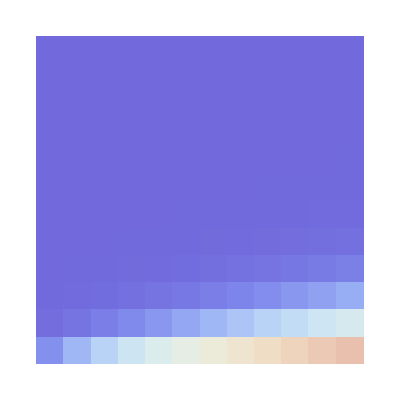
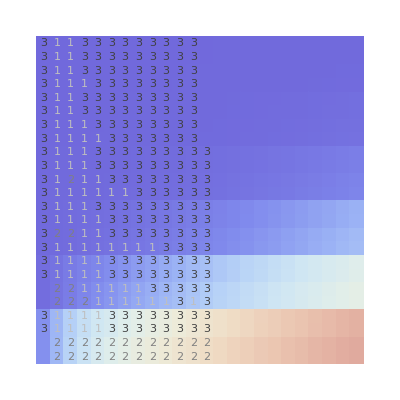
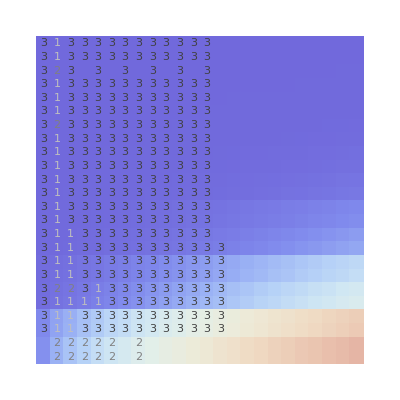
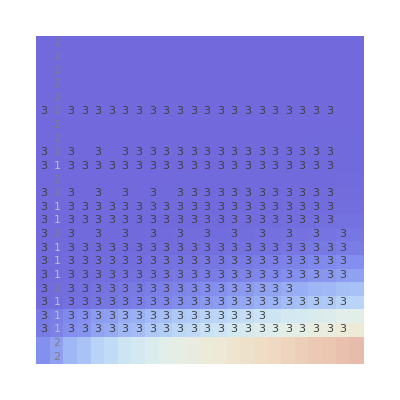
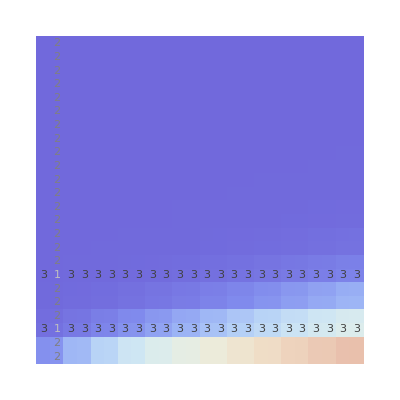
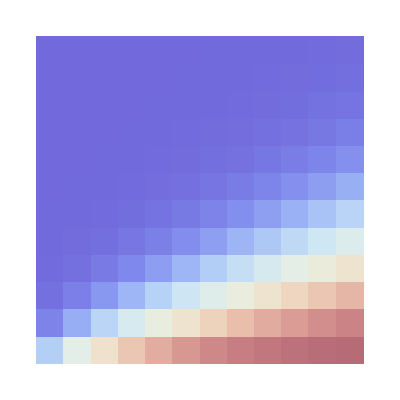
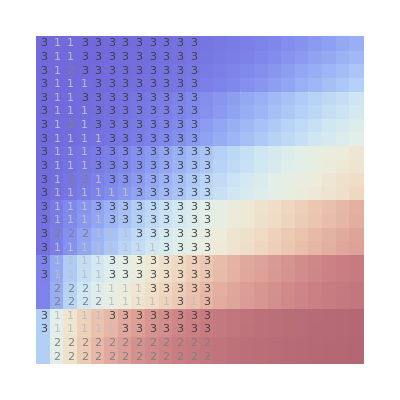
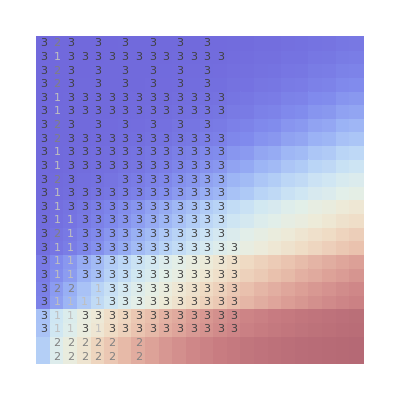

```mathematica
gset
```

```mathematica
If[large == 1, 
Export["optimal-strategies-"<>ToString[amplify]<>"-large.svg", GraphicsGrid[gset], ImageSize->3000]
,
Export["optimal-strategies-"<>ToString[amplify]<>"-.svg", GraphicsGrid[gset], ImageSize->1000]
];
```